# Mat: 150 -- Lab 5

## Francis’s Algorithm

Date: 10/30/2017
Due: 11/6/2017

## Introduction

The QR algorithm is essentially subspace iteration on {e1,e2,...,en} with a change of coordinate system after each iteration. Our first example will involve the symmetric matrix below. Note that we are first creating a random 5x5 matrix whose entries are normally distributed in the interval [-1,1].

```mathematica
A1=RandomVariate[NormalDistribution[-1,1],{5,5}];
A1=Transpose[A1].A1;
```

The function below will perform a change of coordinate system by taking the QR decomposition of A and returning the similarity transformation QAQ*. Here the * denotes the transpose of the matrix, in general it denotes the conjugate transpose, but since we are working in real arithmetic we need not worry about the complex conjugate.

```mathematica
CCS[A_]:=
Module[{Q,R},
{Q,R}=QRDecomposition[A];
R.Transpose[Q]];
```

The function below will perform n iterations of the QR algorithm by performing subspace iteration on {e1,e2,...,en}, doing a change of coordinate system (CCS), and repeating.

```mathematica
QR[A_,n_]:=
Module[{T},
T=A;
Do[T=CCS[T],{i,1,n}];
T];
```

Let’s visualize the QR algorithm using MatrixPlot and Manipulate.

```mathematica
Manipulate[MatrixPlot[QR[A1,n],ColorFunction->"TemperatureMap"],{n,1,20,1}]
```

Note that as n increases the values off the main diagonal tend toward zero (their color gets lighter). We can see from the visual above that the QR decomposition works, but there are some glaring problems. Below we list a few.

At each iteration we are doing matrix multiplication R.Transpose[Q]. Matrix Multiplication is expensive, costing O(n^3) flops. On average, we must perform O(n) iterations to get convergence. Therefore, the QR algorithm is a O(n^4) method. This means that if you double the size of the matrix, it will take 16 times longer to compute the eigenvalues. This is expensive!

Convergence is not fast enough. In the above visual, even after 20 iterations there are some nonzero values below the main diagonal.

## John Francis

John Francis was born near London in 1934. In the late 50’s he was employed by Pegasus computer, where he was responsible for writing linear algebra routines. They were contracted by the military to study the dynamics of aircraft wing design, this required solving for the eigenvalues of a matrix. At this point in time, this was not possible, and some didn’t believe that it would ever be possible. This pessimism was largely due to several factors: limited memory and processing power, no floating point arithmetic standards, and no software. 
At this same time two famous Linear Algebraists, Vera Kublanovskaya and James Wilkinson, were carefully unraveling the mysteries of the eigenvalue problem. In two back-to-back papers  (1961-1962), John Francis put it all together and wrote what we refer to as the Francis’s Algorithm. To this day, Francis’s algorithm is still used to compute the eigenvalues of a matrix, and it was voted in the top 10 algorithms of the 20th century by Dungarra and Sullivan. 
After developing his algorithm, John Francis moved on to compiler development, and his contributions to the scientific community went largely unknown until the early 2000’s. At this time, a group of numerical linear algebraists tracked down John Francis and asked him to give a 1 time talk at the Biennial Numerical Analysis Conference in Glasgow,  Germany in June of 2009. Below are some pictures from that talk.

-Graphics--Graphics-

## The Algorithm

In this section we will highlight the main components of Francis’s algorithm.

### Upper Hessenberg Form

The all important first step of the Francis Algorithm is to first reduce the matrix to Upper Hessenberg Form. 
Fortunately, there is a built in Mathematica function for this task. We will display the result of this function using MatrixPlot below. This time, we will not start with a symmetric matrix.

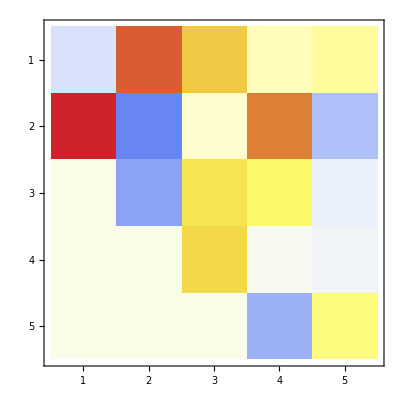

```mathematica
A2=RandomVariate[NormalDistribution[-1,1],{5,5}];
A2=HessenbergDecomposition[A2][[2]];
MatrixPlot[A2,ColorFunction->"TemperatureMap"]
```

Note that everything below the main subdiagonal is zero. Furthermore, the upper Hessenberg form is similar to the original matrix, thus the eigenvalues have been preserved in this transformation.

### Shifts

One way to improve convergence is to shift the eigenvalues of the matrix; thereby isolating the dominate eigenvalue. We do this by picking two shifts s_1 and s_2 and computing the vector P(A)e_1, where P (A) = (A - s_1 I)(A-s_2 I). This was an ingenious aspect of Francis’s algorithm: by using two shifts we can do complex shifts in real arithmetic. Verify for yourself that if s1 and s2 are a complex value and its conjugate pair, then P(A) is real. It is not difficult to write an expression for the matrix vector multiplication P(A)e_1, and we do so below.

```mathematica
SM[A_,s1_,s2_]:=
Module[{x,n},
n=Dimensions[A][[1]];
x=ConstantArray[0,n];
x[[1]]=(A[[1,1]]-s2)*(A[[1,1]]-s1)+A[[2,1]]*A[[1,2]];
x[[2]]=(A[[1,1]]-s2)*A[[2,1]]+A[[2,1]]*(A[[2,2]]-s1);
x[[3]]=A[[2,1]]*A[[3,2]];
Re[x]];
```

Note that I return Re[x], this is because as we noted in the discussion above, even if s1 and s2 are a complex number and its conjugate pair, the resulting vector P(A)e1 should be real. 
Now, what shifts should be chosen is an interesting and detailed topic, but the short answer is that it should be the eigenvalues of the bottom right 2x2 submatrix. The following is a function that will return the eigenvalues of the bottom right 2x2 submatrix of A. Note that I am being lazy here and using the built in function Eigenvalues to return these two eigenvalues.

```mathematica
shifts[A_]:=
Module[{n},
n=Dimensions[A][[1]];
Eigenvalues[A[[n-1;;n,n-1;;n]]]];
```

Next, we need to be able to form an orthogonal matrix Q whose first column is equal to the result of SM[A,s1,s2]. Fortunately, this can be done easily using the QR decomposition. Once we have this Q, we perform a change of coordinate system, and return the resulting matrix to upper Hessenberg form. Then, repeat.

```mathematica
FI[A_]:=
Module[{Q,s1,s2},
{s1,s2}=shifts[A];
Q=IdentityMatrix[Dimensions[A][[1]]]; 
Q[[All,1]]=SM[A,s1,s2];
Q=QRDecomposition[Q][[1]];
HessenbergDecomposition[Q.A.Transpose[Q]][[2]]];
```

We note that the building of Q and the reduction to Hessenberg form can be done with rotations, and this is the key to getting significant cost savings in Francis’s algorithm. However, we are satisfied with the above for the intent of the course. 
We are now ready to see Francis’s Algorithm in action. As an example, consider the code below. At each iteration, we are displaying the MatrixForm, so that we can see the convergence of the algorithm.

```mathematica
Do[A2=FI[A2]; Print[MatrixForm[A2]],{i,1,5}];
```

(-4.70577 | -2.36047 | -0.334821 | 0.752587 | -1.75081
-0.917287 | 1.56089 | -1.02098 | -0.496502 | -0.162021
0. | 2.29448 | 1.88446 | 0.691427 | 1.04463
0. | 0. | 0.311085 | -0.4024 | -1.26345
0. | 0. | 0. | -0.27657 | 0.479166)

(-4.94212 | 1.14353 | 1.74992 | 0.0872821 | 1.88403
0.314553 | 1.99056 | 2.07729 | -0.857526 | 0.534257
0. | -1.0414 | 1.81609 | 0.311036 | 0.157334
0. | 0. | 0.0112875 | -0.849953 | 0.98725
0. | 0. | 0. | -0.0772903 | 0.801771)

(-5.00968 | 1.18678 | 1.36797 | 0.0967879 | -1.86082
-0.0569177 | 1.51025 | -1.21476 | 0.576916 | 0.0241871
0. | 1.95357 | 2.36395 | -0.716106 | -0.629364
0. | 0. | 1.66371×10^-7 | -0.856122 | -0.974664
0. | 0. | 0. | 0.088659 | 0.80795)

(-5.00624 | 1.20997 | 1.34311 | 0.20427 | 1.84936
-0.0180898 | 2.2986 | 2.03014 | -0.728471 | 0.678944
0. | -1.15488 | 1.57216 | 0.510658 | -0.0100565
0. | 0. | 2.81538×10^-15 | -0.80387 | 1.06126
0. | 0. | 0. | -0.00206444 | 0.755698)

(-5.00267 | 0.611896 | 1.71833 | 0.201002 | -1.85094
0.0038389 | 1.37013 | -1.65401 | 0.795235 | 0.32915
0. | 1.5294 | 2.49706 | -0.400837 | -0.588697
0. | 0. | -1.57772×10^-30 | -0.80516 | -1.05935
0. | 0. | 0. | 0.00396979 | 0.756988)

Note that (4,3) entry of the matrix is essentially zero. Therefore, we could solve for the eigenvalues of the bottom right 2x2 submatrix, and continue to solve for the top left 3x3 submatrix.

### Put it all together

In this section, we will walk you through how Francis algorithm would continue on from the example above. First, we would store the eigenvalues of the bottom right 2x2 submatrix (we store all 5 eigenvalues in array called Eigs). Then, we would deflate the problem and only be concerned with the top left 3x3 submatrix. Then, we would proceed to do Francis’s iteration.

```mathematica
Eigs=ConstantArray[0,5];
Eigs[[4;;5]]=Eigenvalues[A2[[4;;5,4;;5]]];
A2=A2[[1;;3,1;;3]];
Do[A2=FI[A2]; Print[MatrixForm[A2]],{i,1,3}];
```

(-5.00282 | -0.913388 | -1.5795
-9.52183×10^-8 | 1.38603 | -1.44593
0. | 1.73642 | 2.48131)

(-5.00282 | 1.49297 | 1.04887
6.04985×10^-17 | 1.69061 | -1.07939
0. | 2.10296 | 2.17673)

(-5.00282 | -1.62359 | -0.832487
1.67235×10^-32 | 1.83999 | -1.0324
0. | 2.14995 | 2.02735)

Now, we see that the top left hand entry must be an eigenvalue, since the (2,1) entry is essentially zero. We deflate, and note that the remaining bottom right submatrix has size 2x2; therefore, we are done.

```mathematica
Eigs[[1]]=A2[[1,1]];
A2=A2[[2;;3,2;;3]];
Eigs[[2;;3]]=Eigenvalues[A2];
Print[Eigs]
```

{-5.00282,1.93367+1.48689 ⅈ,1.93367-1.48689 ⅈ,-0.802464,0.754292}

It is important to note how much faster the convergence of Francis’s algorithm is compared to the QR algorithm that we described earlier. Note that we were able to find all eigenvalues using 8 Francis’s iterations. Using 20 iterations of the QR we still had not found all eigenvalues!

## Assignment

Please do each of the following Problems.

Eventually, deflation will always consists of solving for the eigenvalues of a 2x2 matrix or a 1x1 matrix. Explain why the eigenvalue of a 1x1 matrix is trivial to find, and write a function (call it TE) for solving for the eigenvalues of a 2x2 matrix.

Re-write each function included in the above code, give a brief description of its use, and anywhere where the eigenvalues of a 2x2 matrix are computed use TE from the previous problem.

Create a random 5x5 matrix, as was done in the beginning of the Upper Hessenberg Form Section. Then, run through Francis’s algorithm just as I did, deflating the problem as necessary and storing the corresponding eigenvalues. When you are done, print all of your eigenvalues.